## Finding wave speed

## Define Parameters and Functions

```mathematica
M = 1;
Q = 0;
q = 1;
rEH = M+√(M^2-Q^2);
rmin= 1;
rmax=10;
tmax=10;
f[r_]:=1-(2 M)/r+Q^2/r^2
fprime[r_]:= D[f[r],r]
```

## Define PDE coefficients

```mathematica
coefTT[r_]:= f[r]-2
coefrr[r_]:=f[r]
coefTr[r_]:=2 (1-f[r])
coefT[r_]:= fprime[r]+(2 f[r]+2 ⅈ q Q -2)/r
coefr[r_]:= fprime[r]+(2 f[r]+2 ⅈ q Q)/r
coef[r_]:=(ⅈ q Q)/r^2
```

## Define Ansatz and linear PDE w/ Schwarzschild geometry

```mathematica
Ψ[T_,r_]:=ⅇ^(ⅈ k r -ⅈ w T)
```

```mathematica
eqn[T_,r_]:= coefTT[r] D[Ψ[T,r],{T,2}]+ coefrr[r] D[Ψ[T,r],{r,2}]+coefTr[r] D[D[Ψ[T,r],r],T]-coefT[r]D[Ψ[T,r],T]+coefr[r] D[Ψ[T,r],r] + coef[r] Ψ[T,r]
```

```mathematica
eqn[T,r]
```

-ⅇ^(ⅈ k r-ⅈ T w) k^2 (1-2/r)+ⅈ ⅇ^(ⅈ k r-ⅈ T w) k (2/r^2+(2 (1-2/r))/r)+ⅈ ⅇ^(ⅈ k r-ⅈ T w) (2/r^2+(-2+2 (1-2/r))/r) w+(4 ⅇ^(ⅈ k r-ⅈ T w) k w)/r-ⅇ^(ⅈ k r-ⅈ T w) (-1-2/r) w^2

```mathematica
-ⅇ^(ⅈ k r-ⅈ T w) k^2 (1-2/r)+ⅈ ⅇ^(ⅈ k r-ⅈ T w) k (2/r^2+(2 (1-2/r))/r)+ⅈ ⅇ^(ⅈ k r-ⅈ T w) (2/r^2+(-2+2 (1-2/r))/r) w+(4 ⅇ^(ⅈ k r-ⅈ T w) k w)/r-ⅇ^(ⅈ k r-ⅈ T w) (-1-2/r) w^2
```

-ⅇ^(ⅈ k r-ⅈ T w) k^2 (1-2/r)+ⅈ ⅇ^(ⅈ k r-ⅈ T w) k (2/r^2+(2 (1-2/r))/r)+ⅈ ⅇ^(ⅈ k r-ⅈ T w) (2/r^2+(-2+2 (1-2/r))/r) w+(4 ⅇ^(ⅈ k r-ⅈ T w) k w)/r-ⅇ^(ⅈ k r-ⅈ T w) (-1-2/r) w^2

```mathematica
eqn1[T_,r_]:=Simplify[-ⅇ^(ⅈ k r-ⅈ T w) k^2 (1-2/r)+ⅈ ⅇ^(ⅈ k r-ⅈ T w) k (2/r^2+(2 (1-2/r))/r)+ⅈ ⅇ^(ⅈ k r-ⅈ T w) (2/r^2+(-2+2 (1-2/r))/r) w+(4 ⅇ^(ⅈ k r-ⅈ T w) k w)/r-ⅇ^(ⅈ k r-ⅈ T w) (-1-2/r) w^2]
```

## Solve for w and plot phase velocity

```mathematica
solutions1 = w/.NSolve[eqn[T,r]==0,w]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{(0.5 (-4. k+(0.+2. ⅈ)/r-(1. √(-4.-(0.+8. ⅈ) k r^2-(0.+8. ⅈ) k r^3+4. k^2 r^4))/r))/(2.+r),(0.5 (-4. k+(0.+2. ⅈ)/r+(√(-4.-(0.+8. ⅈ) k r^2-(0.+8. ⅈ) k r^3+4. k^2 r^4))/r))/(2.+r)}

```mathematica
branch1[k_,r_]:= (0.5 (-4. k+(0.+2. ⅈ)/r-(1. √(-4.-(0.+8. ⅈ) k r^2-(0.+8. ⅈ) k r^3+4. k^2 r^4))/r))/(2.+r)
branch2[k_,r_]:= (0.5 (-4. k+(0.+2. ⅈ)/r+(√(-4.-(0.+8. ⅈ) k r^2-(0.+8. ⅈ) k r^3+4. k^2 r^4))/r))/(2.+r)
```

```mathematica
p1=Plot[{Re[branch1[k,2.0]],Im[branch1[k,2.0]],Re[branch1[k,5.0]],Im[branch1[k,5.0]]},{k,0,tmax},PlotRange->All, PlotStyle->{{Dashed,Red},Blue, Orange,Green},PlotLegends->{"Real, r=2.0","Imaginary, r=2.0","Real, r=5.0","Imaginary, r=5.0"},PlotLabel->"Branch 1 ",AxesLabel->{HoldForm[k],HoldForm[w]}];
Export["~/Desktop/wavespeed/p1.png",p1]
```

~/Desktop/wavespeed/p1.png

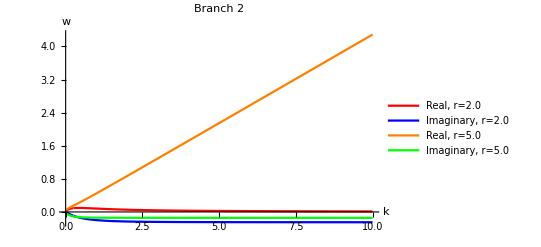

```mathematica
p2=Plot[{Re[branch2[k,2.0]],Im[branch2[k,2.0]],Re[branch2[k,5.0]],Im[branch2[k,5.0]]},{k,0,tmax},PlotRange->All, PlotStyle->{Red,Blue, Orange, Green},PlotLegends->{"Real, r=2.0","Imaginary, r=2.0","Real, r=5.0","Imaginary, r=5.0"},PlotLabel->"Branch 2 ",AxesLabel->{HoldForm[k],HoldForm[w]}]
```

```mathematica
Export["~/Desktop/wavespeed/p2.png",p2]
```

~/Desktop/wavespeed/p2.png

```mathematica
sol11[k_,r_]:=Re[branch1[k,r]]/k
sol12[k_,r_]:=Im[branch1[k,r]]/k
sol21[k_,r_]:=Re[branch2[k,r]]/k
sol22[k_,r_]:=Im[branch2[k,r]]/k
```

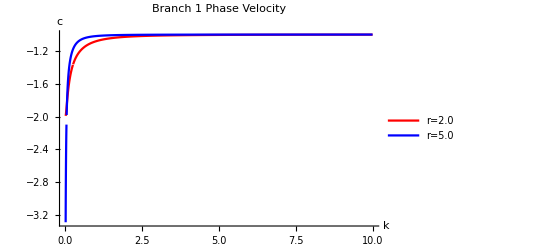

```mathematica
p3=Plot[{sol11[k,2.0],sol11[k,5.0],},{k,0.01,tmax},PlotRange->All, PlotStyle->{Red,Blue},PlotLegends->{"r=2.0","r=5.0"},PlotLabel->"Branch 1 Phase Velocity",AxesLabel->{HoldForm[k],HoldForm[c]}]
```

```mathematica
Export["~/Desktop/wavespeed/p3.png",p3]
```

~/Desktop/wavespeed/p3.png

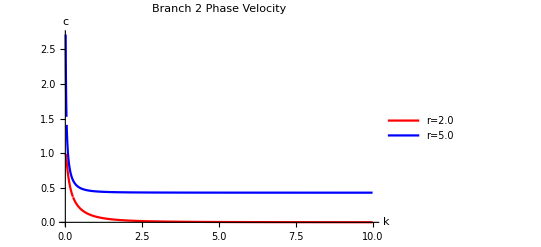

~/Desktop/wavespeed/p4.png

```mathematica
p4=Plot[{sol21[k,2.0],sol21[k,5.0]},{k,0.01,tmax},PlotRange->All, PlotStyle->{Red,Blue},PlotLegends->{"r=2.0","r=5.0"},PlotLabel->"Branch 2 Phase Velocity",AxesLabel->{HoldForm[k],HoldForm[c]}]
Export["~/Desktop/wavespeed/p4.png",p4]
```

```mathematica
Manipulate[Plot[{sol11[k,r],sol12[k,r]},{r,rmin,rmax},PlotRange->All,PlotStyle->{Red,Blue},PlotLegends->{"Real","Imaginary"},PlotLabel->"Phase Velocity Plot: Branch 1",AxesLabel->{HoldForm[r],HoldForm[c]}],{k,0.01,tmax,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[{sol21[k,r],sol22[k,r]},{r,rmin,rmax},PlotRange->All,PlotStyle->{Red,Blue},PlotLegends->{"Real","Imaginary"},PlotLabel->"Phase Velocity Plot: Branch 2",AxesLabel->{HoldForm[r],HoldForm[c]}],{k,0.01,tmax,Appearance->"Labeled"}]
```

```mathematica
Plot3D[sol11[k,r], {k,0.01,10},{r,1,10},PlotRange->All, PlotStyle->Directive[Red,Opacity[0.2]],AxesOrigin->{0,0},AxesLabel->{HoldForm[k],HoldForm[r],HoldForm[c]},PlotLabel->"Phase Velocity Plot 3D: Real Branch 1",LabelStyle->{GrayLevel[0]}]
```

-Graphics3D-

```mathematica
Plot3D[sol12[k,r], {k,0.01,10},{r,1,10},PlotRange->All, PlotStyle->Directive[Blue,Opacity[0.2]],AxesOrigin->{0,0},AxesLabel->{HoldForm[k],HoldForm[r],HoldForm[c]},PlotLabel->"Phase Velocity Plot 3D: Imaginary Branch 1",LabelStyle->{GrayLevel[0]}]
```

-Graphics3D-

```mathematica
Plot3D[sol21[k,r], {k,0.01,10},{r,1,10},PlotStyle->Directive[Red,Opacity[0.2]],PlotRange->All, AxesOrigin->{0,0},AxesLabel->{HoldForm[k],HoldForm[r],HoldForm[c]},PlotLabel->"Phase Velocity Plot 3D: Real Branch 2",LabelStyle->{GrayLevel[0]}]
```

-Graphics3D-

```mathematica
Plot3D[sol22[k,r], {k,0.01,10},{r,1,10},PlotStyle->Directive[Blue,Opacity[0.2]],PlotRange->All, AxesOrigin->{0,0},AxesLabel->{HoldForm[k],HoldForm[r],HoldForm[c]},PlotLabel->"Phase Velocity Plot 3D: Imaginary Branch 2 ",LabelStyle->{GrayLevel[0]}]
```

-Graphics3D-

## Plot Group Velocity

```mathematica
gv11[k_,r_]=Re[D[branch1[k,r],k]];
gv12[k_,r_]=Im[D[branch1[k,r],k]];
gv21[k_,r_]=Re[D[branch2[k,r]k]];
gv22[k_,r_]=Im[D[branch2[k,r],k]];
```

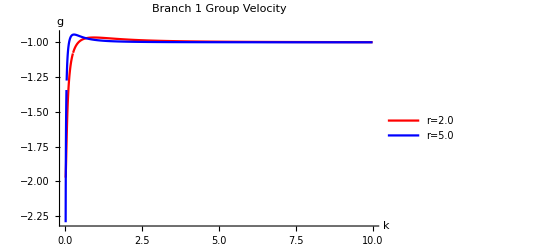

```mathematica
p5=Plot[{gv11[k,2.0],gv11[k,5.0]},{k,0.01,tmax},PlotRange->All, PlotStyle->{Red,Blue},PlotLegends->{"r=2.0","r=5.0"},PlotLabel->"Branch 1 Group Velocity",AxesLabel->{HoldForm[k],HoldForm[g]}]
```

```mathematica
Export["~/Desktop/wavespeed/p5.png",p5]
```

~/Desktop/wavespeed/p5.png

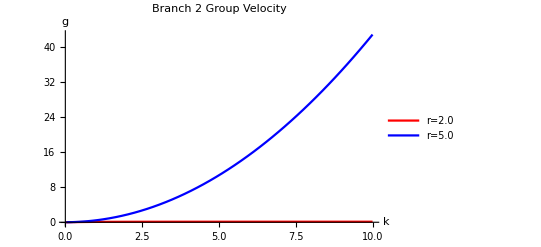

~/Desktop/wavespeed/p6.png

```mathematica
p6=Plot[{gv21[k,2.0],gv21[k,5.0]},{k,0.01,tmax},PlotRange->All, PlotStyle->{Red,Blue},PlotLegends->{"r=2.0","r=5.0"},PlotLabel->"Branch 2 Group Velocity",AxesLabel->{HoldForm[k],HoldForm[g]}]
Export["~/Desktop/wavespeed/p6.png",p6]
```

```mathematica
Manipulate[Plot[{gv11[k,r],gv12[k,r]},{r,rmin,rmax},PlotRange->All,PlotStyle->{Red,Blue},PlotLegends->{"Real","Imaginary"},PlotLabel->"Group Velocity Plot: Branch 1",AxesLabel->{HoldForm[r],HoldForm[g]}],{k,1,tmax,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[{gv21[k,r],gv22[k,r]},{r,rmin,rmax},PlotRange->All,PlotStyle->{Red,Blue},PlotLegends->{"Real","Imaginary"},PlotLabel->"Group Velocity Plot: Branch 2",AxesLabel->{HoldForm[r],HoldForm[g]}],{k,1,tmax,Appearance->"Labeled"}]
```

```mathematica
Plot3D[{gv11 [k,r],gv12[k,r]},{k,0.01,10},{r,1,10},PlotStyle->{Directive[Red,Opacity[0.2]],Directive[Blue,Opacity[0.5]]},PlotLegends->{"Real","Imaginary"},PlotRange->All, AxesOrigin->{0,0},AxesLabel->{HoldForm[k],HoldForm[r],HoldForm[g]},PlotLabel->"Group Velocity Plot 3D: Branch 1",LabelStyle->{GrayLevel[0]}]
```

-Graphics3D-

```mathematica
Plot3D[gv21[k,r] ,{k,0.01,10},{r,1,10},PlotStyle->Directive[Red,Opacity[0.2]],PlotRange->All, AxesOrigin->{0,0},AxesLabel->{HoldForm[k],HoldForm[r],HoldForm[g]},PlotLabel->"Group Velocity Plot 3D: Real Branch 2",LabelStyle->{GrayLevel[0]}]
```

-Graphics3D-

```mathematica
Plot3D[gv22[k,r] ,{k,0.01,10},{r,1,10},PlotStyle->Directive[Blue,Opacity[0.2]],PlotRange->All, AxesOrigin->{0,0},AxesLabel->{HoldForm[k],HoldForm[r],HoldForm[c]},PlotLabel->"Group Velocity Plot 3D: Imaginary Branch 2",LabelStyle->{GrayLevel[0]}]
```

-Graphics3D-

## Expansion of Branches

```mathematica
Series[branch1[k,rEH],{k,0,3}]
```

Piecewise[{{(1.+0. ⅈ) k-(0.+8. ⅈ) k^2-(96.+0. ⅈ) k^3+O[k]^4, Im[(0.-96. ⅈ) k+64. k^2]≥0}, {(0.+0.25 ⅈ)-(2.+0. ⅈ) k+(0.+8. ⅈ) k^2+(96.+0. ⅈ) k^3+O[k]^4, True}}]

```mathematica
Series[branch2[k,rEH],{k,0,3}]
```

Piecewise[{{(1.+0. ⅈ) k-(0.+8. ⅈ) k^2-(96.+0. ⅈ) k^3+O[k]^4, Im[(0.-96. ⅈ) k+64. k^2]<0}, {(0.+0.25 ⅈ)-(2.+0. ⅈ) k+(0.+8. ⅈ) k^2+(96.+0. ⅈ) k^3+O[k]^4, True}}]

## Redefine PDE w/ nonlinear term and Reissner-Nordström geometry

```mathematica
Clear[Q];
```

```mathematica
eqnnonlinear[T_,r_]:= coefTT[r] D[Ψ[T,r],{T,2}]+ coefrr[r] D[Ψ[T,r],{r,2}]+coefTr[r] D[D[Ψ[T,r],r],T]-coefT[r]D[Ψ[T,r],T]+coefr[r] D[Ψ[T,r],r] + coef[r] Ψ[T,r] -λ Ψ[T,r]
```

## Solve for w and plot phase velocity

```mathematica
solutionsnonlinear = w/.NSolve[eqnnonlinear[T,r]==0,w]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{1/(Q^2-2. r-1. r^2)0.5 ((0.-2. ⅈ)-2. k Q^2+4. k r-2. Q r-1. √(-4.+(0.+4. ⅈ) Q^3+(0.+8. ⅈ) k Q^2 r-(0.+8. ⅈ) k r^2-(0.+4. ⅈ) Q r^2+4. Q^2 r^2-(0.+8. ⅈ) k r^3+8. k Q r^3+4. k^2 r^4-4. Q^2 r^2 λ+8. r^3 λ+4. r^4 λ)),1/(Q^2-2. r-1. r^2)0.5 ((0.-2. ⅈ)-2. k Q^2+4. k r-2. Q r+√(-4.+(0.+4. ⅈ) Q^3+(0.+8. ⅈ) k Q^2 r-(0.+8. ⅈ) k r^2-(0.+4. ⅈ) Q r^2+4. Q^2 r^2-(0.+8. ⅈ) k r^3+8. k Q r^3+4. k^2 r^4-4. Q^2 r^2 λ+8. r^3 λ+4. r^4 λ))}

```mathematica
branch1nonlinear[k_,r_,Q_,λ_]:= 1/(Q^2-2. r-1. r^2)0.5 ((0.-2. ⅈ)-2. k Q^2+4. k r-2. Q r-1. √(-4.+(0.+4. ⅈ) Q^3+(0.+8. ⅈ) k Q^2 r-(0.+8. ⅈ) k r^2-(0.+4. ⅈ) Q r^2+4. Q^2 r^2-(0.+8. ⅈ) k r^3+8. k Q r^3+4. k^2 r^4-4. Q^2 r^2 λ+8. r^3 λ+4. r^4 λ))
branch2nonlinear[k_,r_,Q_, λ_]:= 1/(Q^2-2. r-1. r^2)0.5 ((0.-2. ⅈ)-2. k Q^2+4. k r-2. Q r+√(-4.+(0.+4. ⅈ) Q^3+(0.+8. ⅈ) k Q^2 r-(0.+8. ⅈ) k r^2-(0.+4. ⅈ) Q r^2+4. Q^2 r^2-(0.+8. ⅈ) k r^3+8. k Q r^3+4. k^2 r^4-4. Q^2 r^2 λ+8. r^3 λ+4. r^4 λ))
```

```mathematica
solnonlinear11[k_,r_,Q_,λ_]:=Re[branch1nonlinear[k,r,Q,λ]]/k
solnonlinear12[k_,r_,Q_,λ_]:=Im[branch1nonlinear[k,r,Q,λ]]/k
solnonlinear21[k_,r_,Q_,λ_]:=Re[branch2nonlinear[k,r,Q,λ]]/k
solnonlinear22[k_,r_,Q_,λ_]:=Im[branch2nonlinear[k,r,Q,λ]]/k
```

```mathematica
Manipulate[Plot[{solnonlinear11[k,2.0,Q,1.0],solnonlinear12[k,2.0,Q,1.0]},{k,0.01,tmax},PlotRange->All,PlotLegends->{"Real","Imaginary"},PlotLabel->"Branch 1 Nonlinear Phase Velocity: r=2, λ=1",AxesLabel->{HoldForm[k],HoldForm[c]}],{Q,0,1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[{solnonlinear21[k,2.0,Q,1.0],solnonlinear22[k,2.0,Q,1.0]},{k,0.01,tmax},PlotRange->All,PlotLegends->{"Real","Imaginary"},PlotLabel->"Branch 2 Nonlinear Phase Velocity: r=2, λ=1",AxesLabel->{HoldForm[k],HoldForm[c]}],{Q,0,1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[{solnonlinear11[k,2.0,0.0,λ],solnonlinear12[k,2.0,0.0,λ]},{k,0.01,tmax},PlotRange->All,PlotLegends->{"Real","Imaginary"},PlotLabel->"Branch 1 Nonlinear Phase Velocity: r=2, Q=0",AxesLabel->{HoldForm[k],HoldForm[c]}],{λ,0,1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[{solnonlinear21[k,2.0,0.0,λ],solnonlinear22[k,2.0,0.0,λ]},{k,0.01,tmax},PlotRange->All,PlotLegends->{"Real","Imaginary"},PlotLabel->"Branch 2 Nonlinear Phase Velocity: r=2, Q=0",AxesLabel->{HoldForm[k],HoldForm[c]}],{λ,0,1,Appearance->"Labeled"}]
```

## Plot Nonlinear Group Velocity

```mathematica
gvnonlinear11[k_,r_,Q_,λ_]=Re[D[branch1nonlinear[k,r,Q,λ],k]];
gvnonlinear21[k_,r_,Q_,λ_]=Re[D[branch2nonlinear[k,r,Q,λ]k]];
```

```mathematica
Manipulate[Plot[{gvnonlinear11[k,2.0,Q,0.5],gvnonlinear11[k,2.0,Q,1.0]},{k,0.01,tmax},PlotRange->All,PlotLegends->{"λ=0.5","λ=1"},PlotLabel->"Branch 1 Nonlinear Group Velocity: r=2",AxesLabel->{HoldForm[k],HoldForm[g]}],{Q,0,1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[{gvnonlinear21[k,2.0,Q,0.5],gvnonlinear21[k,2.0,Q,1.0]},{k,0.01,tmax},PlotRange->All,PlotLegends->{"λ=0.5","λ=1"},PlotStyle->{Blue,Dashed},PlotLabel->"Branch 2 Nonlinear Group Velocity: r=2",AxesLabel->{HoldForm[k],HoldForm[g]}],{Q,0,1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[{gvnonlinear11[k,2.0,0.0,λ],gvnonlinear11[k,2.0,0.5,λ]},{k,0.01,tmax},PlotRange->All,PlotLegends->{"Q=0.0","Q=0.5"},PlotLabel->"Branch 1 Nonlinear Group Velocity: r=2",AxesLabel->{HoldForm[k],HoldForm[g]}],{λ,0,1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[{gvnonlinear21[k,2.0,0.0,λ],gvnonlinear21[k,2.0,0.5,λ]},{k,0.01,tmax},PlotRange->All,PlotLegends->{"Q=0.0","Q=0.5"},PlotStyle->{Blue,Dashed},PlotLabel->"Branch 2 Nonlinear Group Velocity: r=2",AxesLabel->{HoldForm[k],HoldForm[g]}],{λ,0,1,Appearance->"Labeled"}]
```